Montage to Frequent Colours
Ian Milligan - 2014

This program takes a montage - created using ImageMagick, and extracts the frequent colours. Colours are tricky, so it bins them into relatively consistant ones.

```mathematica
imgColorArea[inputfile_]:=Block[{counts,totalPixels,file},
file=Import[inputfile];
totalPixels=Apply[Times,ImageDimensions[file]];
counts=Tally[Flatten[ImageData[file]/.{r_,g_,b_,a_}->{r,g,b},1],
(Norm[#-#2]<tolerance)&];
#/{1,totalPixels}&/@Reverse[SortBy[counts,Last]]]
```

```mathematica
colorLabeledChart[colordata_]:=
BarChart[colordata[[All,2]],
ChartStyle->RGBColor/@colordata[[All,1]],
ChartLabels->
(Rotate[Style[colorName[#],18],1.5]&/@
colordata[[All,1]]),Axes->{True,False}];
```

```mathematica
combineColorAreas[data_]:=
Reverse[
SortBy[{Mean[#[[All,1]]],Total[#[[All,2]]]}&/@
Gather[Flatten[data,1],(Norm[#[[1]]-#2[[1]]]<0.4)&],
Last]]
```

```mathematica
montage=Import["/users/ianmilligan1/desktop/me.jpg"];
```

```mathematica
colorz=imgColorArea["/Users/ianmilligan1/dropbox/research/Brock-Computer-Vision/Montages/remaps/2-GEOCITIES-ENCHANTEDFOREST-UNIFORM.jpg"];
```

```mathematica
results=colorLabeledChart[colorz]
```

```mathematica
colorz2=imgColorArea["/Users/ianmilligan1/dropbox/research/Brock-Computer-Vision/Montages/remaps/1-CA-REMAP-UNIFORM.png"];
results2=colorLabeledChart[colorz2]
```

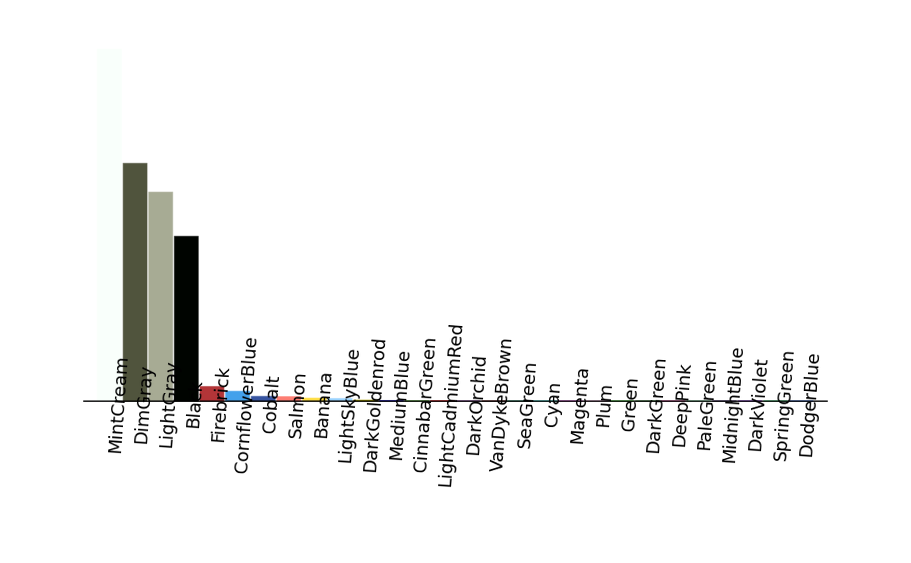
```mathematica
test=-Graphics-
```

-Graphics-

```mathematica
(* When I come in, re-run these for CN, Education, etc. Basically set up a whole shebang process, do the shitload and call ita  week. :) *)
```

```mathematica
? Put
```

expr>>filename writes expr to a file. 
Put[expr_1,expr_2,…,filename] writes a sequence of expressions expr_i to a file. 
Put[filename] creates an empty file with the specified name.

```mathematica
Put[test,"/users/ianmilligan1/desktop/put.mma"]
```